Todo :
Add retroreflected beam (with shifted focus)

# Calculation of lattice beam potential near the surface

Instructions : Run the whole notebook. Results are in the appropriate section.

## Parameter Setup

```mathematica
xFocusDisplacement = 3000;
yFocusDisplacement = 0;
latImbal=0;

xBeamAngle=10.99 Degree;
yBeamAngle=10.95 Degree;

(*zPeak = 24*0.532;(*for horizontal polarization*)*)
zPeak = 21*0.532;(*for vertical polarization*)
zUpper=zPeak-0.5*0.532;
zLower=zPeak+0.5*0.532;

xLongWaist=40;
xTransWaist=135;
yLongWaist=40;
yTransWaist=135;
```

## Calculation

General notes:
Distances are measured in micrometers. The positive z direction is pointing downwards, away from the substrate in calculations.
See also: Siegman: Lasers, Ch.16

### Function definitions

```mathematica
gaussianEOld[x_, y_, z_, wx_, wy_]:= Module[{λ=1.064,k, zRayleighX, zRayleighY, localWaistX, localWaistY, invRCurvatureX, invRCurvatureY},
k= 2 π/λ;
zRayleighX= π wx^2/λ;
zRayleighY= π wy^2/λ;
localWaistX=wx Sqrt[1+(z/zRayleighX)^2];
localWaistY=wy Sqrt[1+(z/zRayleighY)^2];
invRCurvatureX=z/(z^2+zRayleighX^2);
invRCurvatureY=z/(z^2+zRayleighY^2);
Sqrt[(wx wy)/(localWaistX localWaistY)]Exp[-x^2/localWaistX^2 -y^2/localWaistY^2] Exp[-I k (z+x^2 invRCurvatureX/2 + y^2 invRCurvatureY/2)]]
gaussianE[x_,y_,z_,wx_,wy_]:=Module[{λ=1.064,k,complexRadiusX,complexRadiusY},k= 2 π/λ;
complexRadiusX=z-I k wx^2/2;complexRadiusY=z-I k wy^2/2;
Sqrt[(-I k wx^2/2)/complexRadiusX ] Sqrt[(-I k wy^2/2)/complexRadiusY] Exp[I k z+I k (x^2/complexRadiusX+y^2/complexRadiusY)]
]
reflectedBeamEHorizontal[x_,y_, z_, θ_, wx_, wy_,focusDisplacement_] := Module[{xBeamIncoming=x Sin[θ] + z Cos[θ], zBeamIncoming=x Cos[θ]-z Sin[θ]-focusDisplacement, phaseShiftOutgoing = -1, xBeamOutgoing = -x Sin[θ]+z Cos[θ], zBeamOutgoing=x Cos[θ]+z Sin[θ]-focusDisplacement}, gaussianE[xBeamIncoming,y,  zBeamIncoming, wx, wy] + phaseShiftOutgoing*gaussianE[xBeamOutgoing,y, zBeamOutgoing, wx, wy]]
reflectedBeamEVertical[x_,y_, z_, θ_, wx_, wy_,focusDisplacement_] := Module[{xBeamIncoming=x Sin[θ] + z Cos[θ], zBeamIncoming=x Cos[θ]-z Sin[θ]-focusDisplacement, phaseShiftOutgoing = 1, xBeamOutgoing = -x Sin[θ]+z Cos[θ], zBeamOutgoing=x Cos[θ]+z Sin[θ]-focusDisplacement}, gaussianE[xBeamIncoming,y,  zBeamIncoming, wx, wy]{-Sin[θ],Cos[θ]}+ phaseShiftOutgoing*gaussianE[xBeamOutgoing,y, zBeamOutgoing, wx, wy]]{Sin[θ],Cos[θ]}
reflectedBeamIHorizontal[x_,y_,  z_, θ_, wx_, wy_,focusDisplacement_] := Abs[reflectedBeamEHorizontal[x,y, z, θ,wx, wy,focusDisplacement]]^2
reflectedBeamIVertical[x_,y_,  z_, θ_, wx_, wy_,focusDisplacement_] := Norm[reflectedBeamEVertical[x,y, z, θ,wx, wy,focusDisplacement]]^2
```

### Calculations

Beams

```mathematica
xBeamPotential[x_, y_, z_] := reflectedBeamIVertical[x,y,z,xBeamAngle,xLongWaist,xTransWaist,xFocusDisplacement]
yBeamPotential[x_, y_, z_] := reflectedBeamIVertical[y,x,z,yBeamAngle,yLongWaist,yTransWaist,yFocusDisplacement]
xMaxFull = FindMaximum[{xBeamPotential[x,0,z], {x∈Reals,z>11, z<12}},{{x,0},{z, 12.7685}}];//Quiet
xMaxVal = xMaxFull[[1]];
xMaxRules=xMaxFull[[2]];
xxMaxLoc=x/.xMaxRules;
xzMaxLoc=z/.xMaxRules;
yMaxFull = FindMaximum[{yBeamPotential[0,y,z],{y∈Reals, z>11, z<12}},{{y,0},{z, 12.7685}}];//Quiet
yMaxVal = yMaxFull[[1]];
yMaxRules=yMaxFull[[2]];
yyMaxLoc=y/.yMaxRules;
yzMaxLoc=z/.yMaxRules;

xZMax[x_] := Quiet[Module[{z},z/. FindMaximum[{xBeamPotential[x,0,z], {z>11, z<12}},{{z, xzMaxLoc}}][[2]]]];
yZMax[y_] := Quiet[Module[{z},z/. FindMaximum[{yBeamPotential[0,y,z],{z>11,z<12}},{{z,yzMaxLoc}}][[2]]]];
```

Combined potential and gradient

```mathematica
totalPotentialWithZ[x_,y_,z_]:=((1+Max[0,latImbal])xBeamPotential[x+xxMaxLoc,y,z]/(2*xMaxVal)) +((1+Max[0,-latImbal])yBeamPotential[x,y+yyMaxLoc,z]/(2*yMaxVal));
totalPotentialHorizontal[x_,y_]:=totalPotentialWithZ[x,y,zPeak];
totalGradient[x_,y_]:=totalPotentialWithZ[x,y,zUpper]-totalPotentialWithZ[x,y,zLower];
```

### Intermediate results for debugging

```mathematica
Echo[{xMaxVal, xMaxRules}, "{Max potential depth of X lattice beam, Location of maximum} ="];
Echo[{yMaxVal, yMaxRules}, "{Max potential depth of Y lattice beam, Location of maximum} ="];
```

{Max potential depth of X lattice beam, Location of maximum} = {2.59326,{x→2.70899,z→11.1417}}

{Max potential depth of Y lattice beam, Location of maximum} = {2.81729,{y→1.51833,z→11.1813}}

## Results

Potential of the X Lattice beam along the beam and perpendicular to the substrate

```mathematica
DensityPlot[xBeamPotential[x,0,-z], {x,-20,20}, {z,-15,0}, PlotRange->Full, PlotPoints->100, Frame->True, FrameLabel->{"x [um]", "z [um]"}, ImageSize->400, LabelStyle->20]
```

-Graphics-

Vertical position of X lattice beam power maximum along the beam centered at the beam maximum

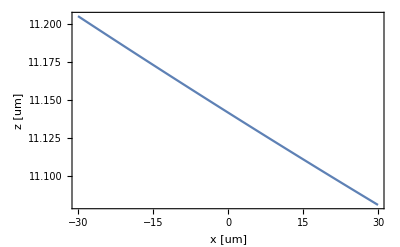

```mathematica
Plot[xZMax[x+xxMaxLoc], {x, -30, 30},PlotRange->Full, Frame->True, FrameLabel->{"x [um]", "z [um]"}, ImageSize->400, LabelStyle->20]
```

Vertical position of Y lattice beam power maximum along the beam centered at the beam maximum

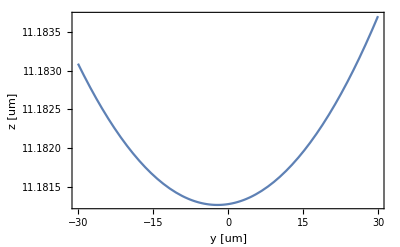

```mathematica
Plot[yZMax[(y+yyMaxLoc/.yMaxRules)], {y, -30, 30},PlotRange->Full, Frame->True, FrameLabel->{"y [um]", "z [um]"}, ImageSize->400, LabelStyle->20]
```

The lattice potential in red centered at the dimple location

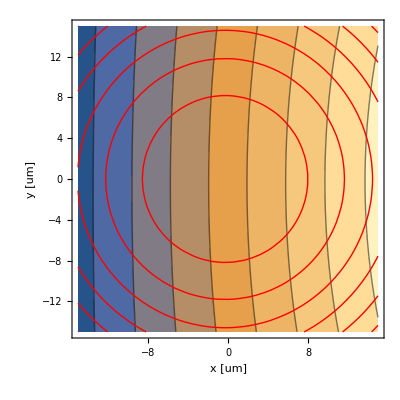

```mathematica
imgPotential=ContourPlot[totalPotentialHorizontal[x,y],{x, -15, 15}, {y, -15, 15}, PlotRange->Full,ContourShading->None, ContourStyle->Red, Frame->True, FrameLabel->{"x [um]", "y [um]"}, ImageSize->400, LabelStyle->20];
imgGradient=ContourPlot[totalGradient[x,y],{x, -15, 15}, {y, -15, 15}, PlotRange->Full, Frame->True, FrameLabel->{"x [um]", "y [um]"}, ImageSize->400, LabelStyle->20];
Show[{imgGradient,imgPotential}]
```

```mathematica
11.35/0.532
```

21.3346

```mathematica
21*0.532
```

11.172